comparison of the sum for susceptibility and its exact formula

```mathematica
datS =Table[Table[N[(1/2) Sum[Sin[k r Pi/(n+1)]Sin[k s Pi/(n+1)]/Sin[k Pi/(2(n+1))]^2,{k,1,n}]],{s,1,Floor[n/2]},{r,s,n}],{n,4,10}];
```

```mathematica
datS =Table[Table[N[(1/2) Sum[Sin[k r Pi/(n+1)]Sin[k s Pi/(n+1)]/Sin[k Pi/(2(n+1))]^2,{k,1,n}]],{s,1,Floor[n/2]},{r,s,n}],{n,4,10}];
```

```mathematica
datE =Table[Table[N[(n+1)Min[r,s]-r s],{s,1,Floor[n/2]},{r,s,n}],{n,4,10}];
```

```mathematica
Chop[datS-datE]
```

{{{0,0,0,0},{0,0,0}},{{0,0,0,0,0},{0,0,0,0}},{{0,0,0,0,0,0},{0,0,0,0,0},{0,0,0,0}},{{0,0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0}}}

Approximate expression for F:

```mathematica
invF = Exp[Sum[Cos[k Pi/(2(n+1))]^2/Sin[k Pi/(2(n+1))],{k,1,n}]/(4(n+1))]
```

ⅇ^((∑_(k=1)^n Cos[(k π)/(2 (1+n))] Cot[(k π)/(2 (1+n))])/(4 (1+n)))

The sum can be approximated by an integration. Consider a change of variables x = k/(n+1)

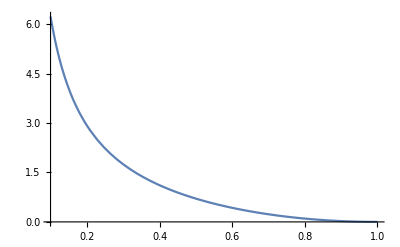

```mathematica
Plot[Cos[x Pi/2]^2/Sin[x Pi/2],{x,0.1,1}]
```

The lower bound is:

```mathematica
Integrate[Cos[x Pi/2]^2/(4Sin[x Pi/2]),{x,1/(n+1),1},Assumptions->n>1]
```

-(Cos[π/(2+2 n)]+Log[Tan[π/(4+4 n)]])/(2 π)

This inspires a scaling (n+1)^(-1/2Pi)

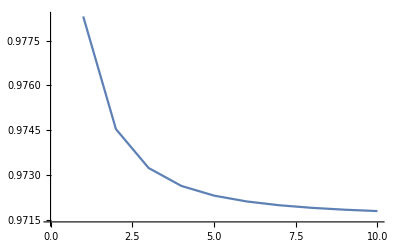

```mathematica
ListLinePlot[Table[N[invF (n+1)^(-1/(2Pi))],{n,1,10}]]
```

We do not prove monotonicity, but the limits are:

```mathematica
N[invF (n+1)^(-1/(2Pi))/.{n->1}]
```

0.978309

```mathematica
N[invF (n+1)^(-1/(2Pi))/.{n->10000}]
```

0.97157

```mathematica
invF (n+1)^(-1/(2Pi))/.{n->1}
```

2^(-1/2/π) ⅇ^(1/(8 √2))

```mathematica
Series[HarmonicNumber[k-1]/(2 π),{k,Infinity,2}]
```

(EulerGamma+Log[k])/(2 π)-1/(4 π k)-1/(24 π k^2)+O[1/k]^3

```mathematica
Integrate[Cos[x Pi/2]^2/Sin[x Pi/2] - 2/(Pi x),{x,0,1}]/4
```

-(1+Log[π/4])/(2 π)

```mathematica
N[Exp[EulerGamma/(2 π)-(1+Log[π/4])/(2 π)]]
```

0.97157

```mathematica
Simplify[Exp[EulerGamma/(2 π)-(1+Log[π/4])/(2 π)]]
```

ⅇ^((-1+EulerGamma+Log[4/π])/(2 π))

```mathematica
N[Exp[EulerGamma/(2 π)-(1+Log[π/4])/(2 π)]-2^(-1/2/π) ⅇ^(1/(8 √2))]
```

-0.00673933